# 医学生物学分野における高被引用論文の長期変化

## 要旨

PubMedの3000万件を超える収録記事を対象として、高被引用論文の変遷を、これにかかる雑誌や研究テーマの変遷とともに調査した。

## 背景

一般的に論文評価の研究では評価の公正性の面より出版から特定の期間の被引用が用いられる。一方別の観点からはオブソレッセンスに注目することもある。つまり、実際の引用では古く出版された論文ほど有利になるが、オブソレッセンスにより次第に引用されなくなり、いずれは世代交代が行われる。本研究は長期にわたる大規模な引用関係を分析することにより、実際のオブソレッセンス現象を確認する。ここでのオブソレッセンスとは単にインパクトの長期変化だけではなく研究テーマの変遷等も含む広義のもの（トレンド）である。従来、大規模な引用関係の分析は主に雑誌間の関係に注目されることが多かった。これは大規模な引用の要素をまとめる単位として雑誌が適当であることがおもな理由と考えられる。比較的大規模な研究としては、Leydesdorff[1,2,3,4]が雑誌間の関係マップを構築・調査した。天野ら[5,6]は医学生物学雑誌の大規模クラスタリングを行い、分野間の引用関係を明らかにしている。近年ではLiら[7]が長期にわたる引用の特徴を、2300万論文をグループ化して調査した。しかしながら長期にわたる論文の引用関係と研究のトレンドの変化に着目した研究は稀である。そこで本研究ではPubMedのデータを利用し医学生物学分野の高被引用論文に注目し、引用関係の世代ごとの変化を調査した。

高被引用論文は研究のトレンドをよく反映するものと考えられ、またPubMedには各論文に統制語が付与されているため、高被引用論文に付与される統制語を計量的に分析することにより、トレンド変化の特徴を見出せると期待される。また、注目する対象を絞ることにより大規模な引用の要素全体を取り扱うことを回避できる。

## 目的

本研究では医学生物学分野における高被引用論文に注目し、関連するテーマや雑誌の長期変化を明らかにする。ここでは長期的トレンドやオブソレッセンスを捉えるため、世代ごとのデータを累積的に構成する。これにより一過的なトレンドは現れにくくなると期待される。

## Materials

### 1. データ

FTP版のPubmed baseline (2023)[8]を利用した。

### 2. 世代の構成

PubMedに収録されている出版年が1946-2020である論文を対象とした。1946-2020の出版年をオーバーラップなしの5年ごとの区切りとし、15層の世代を構成した。各世代で対象となる被引用論文は Pubmed baseline に収録される最初の出版年（1781）から当該世代までのすべてのタイプの記事となる。これらの世代を累積的に用いる場合には累積世代、個別に用いる場合には単に世代と称する。図表において各世代/累積世代を表す場合には最終年を表記する。

### 3. 主要論文・主要雑誌・主要テーマ

ここで本研究においてはトレンドとして主要論文、主要雑誌、主要テーマに注目する。主要論文とは、本研究タイトルの「高被引用論文」のことであり、各累積世代において被引用数全体の1%を構成する論文集合とする。被引用数の1%に厳密に対応する論文集合の抽出は困難であるため、被引用数の多い順に論文の被引用数を累積し、全引用数の1%に最も近い順位を持つ論文までを対象とした。主要雑誌とは主要論文を出版した雑誌とする。主要テーマとは主要論文に付与されるMeSHの集合とする。さらに主要論文を引用する論文群を考え、これらの論文に付与されるMeSHの集合を主要引用テーマとする。また、主要テーマと主要引用テーマに関しては、比較のため高被引用ではない論文群のテーマについても分析した。これらを「研究テーマ」「引用テーマ」とする。主要テーマは研究テーマの一部であり、主要引用テーマは引用テーマの一部である。

以上の定義を表1にまとめる。

表1

本研究での用語定義

主要論文 | 被引用数全体の1%を構成する被引用数上位論文（集合）。
主要雑誌 | 主要論文を出版した雑誌。
主要テーマ | 主要論文に付与されるMeSH。
主要引用テーマ | 主要論文を引用する論文に付与されるMeSH。
研究テーマ | 論文に付与されるMeSH。主要テーマを含む。
引用テーマ | 論文を引用する論文に付与されるMeSH。主要引用テーマを含む
世代 | 1946 - 2020の期間に対して5年ごとに区切るもの。データを累積的に扱う場合は「累積世代」と表記する。

#### 3.1 テーマの計数

テーマの計数には引用される論文のMeSHをそのままカウントする。一方、研究テーマと引用テーマの関係においては、論文1本とそれを引用する論文1本ごとに被引用側・引用側における完全2部グラフの関係とみなしエッジを分数カウントする。

## Main

### 1. PubMed annual baseline

本研究で用いた2023年のFTP版PubMed annual baselineの各統計を表2に示す。わずかに2024年の論文も含まれている。

図1に出版年ごとの論文収録数を示す。明確な増加が見られる1946年から2020年までに出版された論文およびそれらから引用された論文を本研究の対象とした。

図2に本研究の対象である累積世代ごとの論文数、うち参照を持つ論文数、参照数（述べ）、被引用論文数（ユニーク）、登録雑誌数を示す。登録雑誌数以外は途中から急激な増加を示している。対象とした論文は1946から2020に出版された31,440,632論文とそこから引用される論文である。

表 2

PubMed annual baselineのレコード数

論文数 | 雑誌数 | 最初の論文出版年 | 最後の論文出版年
36,555,430 | 36,943 | 1781 | 2024

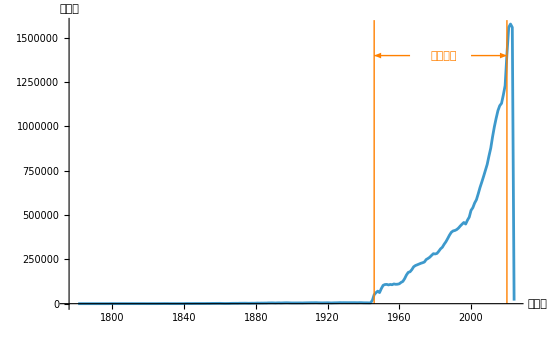

図1

PubMed annual baselineの登録論文数の推移

図 2

1946年以降の累積世代ごとの論文数

累積世代ごとの論文数(articles)、うち参照を持つ論文数(citing articles)、参照数(references)、被引用論文数(cited articles)、および雑誌数(Journal)。

### 2. 累積世代ごとの主要論文の変化

主要論文の出現数を図3に示す。主要論文の全論文に占める割合と、新規主要論文の主要論文に占める割合をそれぞれ、図4、図5に示す。主要論文数および新規出現主要論文数は1946~2010の世代以降に急増している一方、主要論文の全論文に占める割合は一定の傾向を示していないことから、主要論文数の急増は収録論文数の急増を受けてのものであると考えられる。また、新規出現主要論文の主要論文に占める割合についても一定の傾向は読み取れない。

累積世代ごとの最多被引用論文の論文タイトルとその被引用数を表4に示す。主要論文は世代が進んでも引き続き引用され続ける傾向があり、このため累積的変化では複数世代にわたり最多被引用主要論文の交代は少なく、数十年をかけてインパクトを上昇させていることが窺える。いずれの論文のテーマもタンパク質の分析に関するものであり、高被引用論文のテーマには嗜好性があることが示唆される。

表4

累積世代ごとの最多被引用論文タイトル

累積世代 | 論文タイトル | 収録誌タイトル | 被引用数 | 当世代の
主要論文数
1946-1950 | Qualitative analysis of proteins: a partition chromatographic method using paper. | The Biochemical journal | 74 | 10
1946-1955 | Qualitative analysis of proteins: a partition chromatographic method using paper. | The Biochemical journal | 154 | 30
1946-1960 | Protein measurement with the Folin phenol reagent. | The Journal of biological chemistry | 300 | 46
1946-1965 | Protein measurement with the Folin phenol reagent. | The Journal of biological chemistry | 1190 | 50
1946-1970 | Protein measurement with the Folin phenol reagent. | The Journal of biological chemistry | 3876 | 38
1946-1975 | Protein measurement with the Folin phenol reagent. | The Journal of biological chemistry | 9632 | 33
1946-1980 | Protein measurement with the Folin phenol reagent. | The Journal of biological chemistry | 17763 | 32
1946-1985 | Protein measurement with the Folin phenol reagent. | The Journal of biological chemistry | 25451 | 26
1946-1990 | Protein measurement with the Folin phenol reagent. | The Journal of biological chemistry | 32371 | 19
1946-1995 | Protein measurement with the Folin phenol reagent. | The Journal of biological chemistry | 37576 | 22
1946-2000 | Protein measurement with the Folin phenol reagent. | The Journal of biological chemistry | 40229 | 33
1946-2005 | Protein measurement with the Folin phenol reagent. | The Journal of biological chemistry | 42101 | 66
1946-2010 | Protein measurement with the Folin phenol reagent. | The Journal of biological chemistry | 44884 | 192
1946-2015 | Cleavage of structural proteins during the assembly of the head of bacteriophage T4. | Nature | 49961 | 315
1946-2020 | Cleavage of structural proteins during the assembly of the head of bacteriophage T4. | Nature | 54249 | 336

-Graphics-

図3

累積世代ごとの主要論文および新規主要論文の出現数

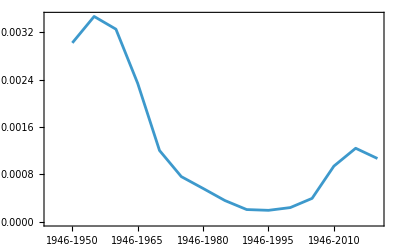

図4

累積世代ごとの主要論文の全論文に占める割合（%）

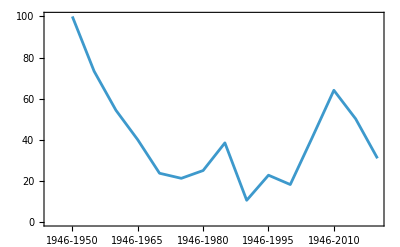

図5

累積世代ごとの新規出現主要論文の主要論文に占める割合（%）

### 3. 累積世代ごとの主要雑誌の変化

主要雑誌の出現数を図6に示す。主要雑誌の全雑誌に占める割合と、新規主要雑誌の主要雑誌に占める割合をそれぞれ、図7、図8に示す。主要雑誌数および新規出現主要論雑誌は1946~2010の世代以降に急増しており、前述した主要論文数の急増のタイミングと一致する。主要雑誌の全雑誌に占める割合および新規出現主要雑誌の主要雑誌に占める割合に一定の傾向は見られないが、主要論文のそれと同様の挙動が見られる。

累積世代ごとの主要論文を出版した雑誌のうち主要論文出版数上位の一覧を表5に示す。主要論文を持つ雑誌は必ずしもインパクトファクターが高い雑誌ではないことがわかる。

表5

累積世代ごとの主要雑誌のうち主要論文の最大数を持つもの

インパクトファクター(IF)とその発表年については当該誌の公式ホームページから求めた。

累積世代 | 雑誌タイトル | 当該誌の
主要論文数 | 当該誌の主要論文が
当該世代主要論文に
占める割合(%) | IF | /IF発表年
1946-1950 | The Journal of clinical investigation
The Biochemical journal | 3
3 | 30 | 13.3 | /2023
4.4 | /2023
1946-1955 | The Biochemical journal | 13 | 43 | 4.4 | /2023
1946-1960 | The Biochemical journal | 11 | 24 | 4.4 | /2023
1946-1965 | The Biochemical journal | 13 | 26 | 4.4 | /2023
1946-1970 | The Biochemical journal | 9 | 24 | 4.4 | /2023
1946-1975 | The Journal of biological chemistry | 7 | 21 | 4. | /2023
1946-1980 | The Journal of biological chemistry | 7 | 22 | 4. | /2023
1946-1985 | The Journal of biological chemistry | 5 | 19 | 4. | /2023
1946-1990 | The Journal of biological chemistry | 4 | 21 | 4. | /2023
1946-1995 | The Journal of biological chemistry | 4 | 18 | 4. | /2023
1946-2000 | Journal of molecular biology
Proceedings of the National Academy of Sciences of the United States of America | 4
4 | 12 | 4.7 | /2023
9.4 | /2023
1946-2005 | Proceedings of the National Academy of Sciences of the United States of America | 8 | 12 | 9.4 | /2023
1946-2010 | Proceedings of the National Academy of Sciences of the United States of America
Nature | 14
14 | 7 | 9.4 | /2023
50.5 | /2023
1946-2015 | Nature | 20 | 6 | 50.5 | /2023
1946-2020 | Bioinformatics (Oxford, England) | 17 | 5 | 4.4 | /2023

-Graphics-

図6

累積世代ごとの主要雑誌および新規主要雑誌の出現数

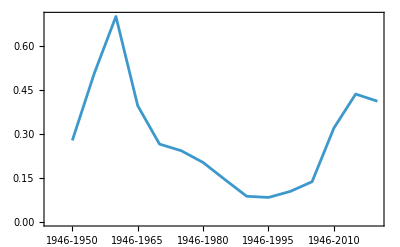

図7

累積世代ごとの主要雑誌の全雑誌に占める割合（%）

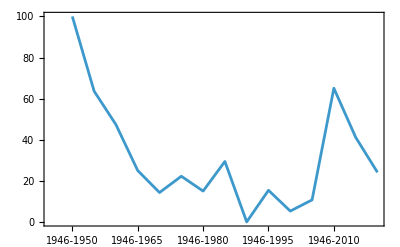

図8

累積世代ごとの新規出現主要雑誌の主要雑誌に占める割合（%）

### 4. 累積世代ごとの主要テーマの変化と特徴

#### 4.1 主要テーマの出現数

累積世代ごとの主要テーマ（MeSHディスクリプター）のユニーク出現数を図9に示す。2023年MeSHディスクリプターの総数はおよそ30000であるが、累積世代における出現数は最大でも3000を超える程度であり集中が見られる。新規出現主要ディスクリプターの主要ディスクリプターに占める割合を図10に示す。累積世代ごとの主要テーマ出現の集中度を見るためにGini係数を求めた。（図11）累積世代が進むにつれ上昇する傾向にあるが最大でも0.6程度となる。

図9

累積世代ごとの主要論文に付与されたMeSHディスクリプターの種数

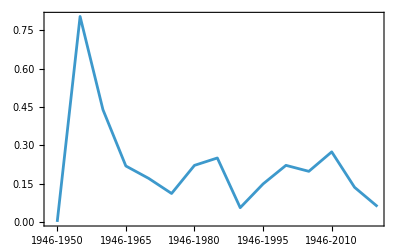

図10

新規出現主要ディスクリプターの主要ディスクリプターに占める割合（%）

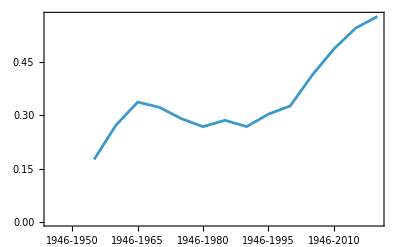

図11

累積世代ごとの主要論文に付与されたMeSHディスクリプターの出現数に関するジニ係数

1946~1950世代では当該ディスクリプターの付与がなかったため値を算出していない。

#### 4.2 主要テーマの変化

ここでは主要テーマの変化を、高被引用でない論文群と比較しながら分析する。全てで4グループを構成するものとし、分割は順位ではなく生産性によるものとした。主要論文はすべての論文の総被引用数の1%を構成する論文群、つまり生産の上位0~1%の論文群であり、これをグループ1（G1）とした。同様に被引用数の25~26%を構成する論文をG2、50~51%を構成する論文をG3、75~76%を構成する論文をG4とした。

テーマの計数については前述したように1論文対1論文の引用強度が1となるようにテーマ間の引用を分数計数とした。

まず、各累積世代、各グループごとの最頻出テーマを表6に示す。最頻出テーマは研究テーマと引用テーマに分けた。最頻出テーマのバラエティは、高被引用グループの研究テーマにのみ見られ、それ以外のテーマはHumansもしくはAnimalsの出現のみであり、最頻出テーマのバラエティは非常に低い。

次に、各累積世代のテーマ全体の多様性の変化を見るためにグループ全体のエントロピーの変化を観察した。図12-1 ~ 図12-3はそれぞれ、研究テーマ、引用テーマ、研究テーマと引用テーマの対の出現数のエントロピーである。図12からは主要論文グループのみが研究テーマのエントロピーが低く、その他のグループ間ではそれほど差がないことがわかる。なお、1946~1950世代に関してはディスクリプターの付与数が十分でなかったため除外している。

また、研究者の引用行動は必ずしも当該論文と同じ分野を引用するものではない。この転換の程度を見るために、グループごとに研究テーマと引用テーマのコサイン距離を観察した。これを図13に示す。こちらも高被引用グループのみが他とは異なる様相を示した。また、高被引用グループにおいても1946~2010世代以降は減少傾向にあり、他グループとの差は累積世代ごとに少なくなっている。さらに、各累積世代の全体的な研究テーマも一定でなく世代ごとの嗜好の影響を受けると考えられる。この転換の程度を確認するために、各グループの累積世代間の研究テーマのコサイン距離を観察した。世代間では論文集合のメンバーが異なるので論文集合全体のテーマの重み付カウントを用いた。値は前世代との距離を表す。これを図14に示す。

以上のテーマの変遷の観察からは以下のことが窺える：(1)高被引用論文は異なるテーマから引用されやすい。このことは表6の最頻出テーマから予想され、図13における転換の値もこれを裏付けている。(2)高被引用論文群は研究テーマが集中的であり、それを引用する論文群の研究テーマもまた集中的である。このことは図12-1、2から窺える。(3)また、図14から、全体として研究テーマは各累積世代ごとに変遷がありその程度の傾向も一定ではない。グループ2のみが常に低いテーマ転換を保っていることから、被引用において中庸な一部の論文群においてはそのテーマが安定的である可能性が高い。

表6

累積世代ごと論文グループごとの最頻出テーマ

Citingは引用テーマ、Citedは研究テーマを示す。

1946-1955
1946-1960
1946-1965
1946-1970
1946-1975
1946-1980
1946-1985
1946-1990
1946-1995
1946-2000
1946-2005
1946-2010
1946-2015
1946-2020 | G1
Citing | 
Cited
Humans | Insulin
Humans | Blood Proteins
Animals | Microscopy, Electron
Animals | Microscopy, Electron
Animals | Microscopy, Electron
Animals | Proteins
Animals | Proteins
Animals | Proteins
Animals | Base Sequence
Animals | Base Sequence
Animals | Base Sequence
Animals | Humans
Humans | Humans
Humans | Humans | G2
Citing | 
Cited
Humans | Humans
Humans | Humans
Humans | Humans
Humans | Humans
Humans | Humans
Humans | Humans
Animals | Humans
Animals | Animals
Animals | Humans
Animals | Animals
Humans | Animals
Humans | Humans
Humans | Humans
Humans | Humans | G3
Citing | 
Cited
Humans | Humans
Humans | Humans
Humans | Humans
Humans | Humans
Humans | Humans
Humans | Humans
Humans | Animals
Humans | Humans
Humans | Humans
Humans | Humans
Humans | Humans
Humans | Humans
Humans | Humans
Humans | Humans | G4
Citing | 
Cited
Humans | Humans
Humans | Humans
Humans | Humans
Humans | Humans
Humans | Animals
Humans | Humans
Humans | Humans
Humans | Humans
Humans | Humans
Humans | Humans
Humans | Humans
Humans | Humans
Humans | Humans
Humans | Humans

-Graphics--Graphics--Graphics-

図12

累積世代、論文グループごとのMeSHディスクリプターの出現に関するエントロピー

1946~1950世代では十分なディスクリプターの付与がなかったため対象外とした。

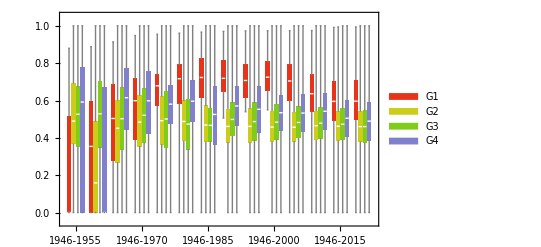

図13

累積世代、論文グループごとの研究テーマに対する引用テーマの転換

論文に付与されたディスクリプターとその論文を引用する論文に付与されたディスクリプター出現数のコサイン距離。箱ひげ図の区間は、下から最小値、25%分位点、中央値、75%分位点、最大値となる。1946~1950世代では十分なディスクリプターの付与がなかったため対象外とした。

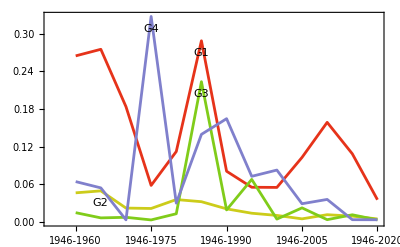

図14

累積世代、論文グループごとの論文集合における累積世代間の研究テーマの転換

1946~1950世代では十分なディスクリプターの付与がなかったため対象外とした。

### 5. 主要論文のオブソレッセンス

各累積世代の主要論文の総数は536であったが、十分にオブソレッセンスが観察される論文を選択するために次の3つの条件を設定した： 1. 出版年から十分な期間がある、2. ピーク期が十分に過ぎ去っている、3. 被引用の傾向が十分に低下しているもの。以上の条件は、P.D.B Paroloら[]およびD. Wangら[]のオブソレッセンスモデルに基づく（図15）。この結果77論文が選択された。以降、これらの論文を主要obsolete論文と呼ぶこととする。

図16に主要obsolete論文の出版からの経過年ごとの被引用数を表す。出版からの経過年は最小で10年、最大で84年であった。図17に主要obsolete論文の出版からピークまでの年、ピークから減衰するまでの年、出版から減衰するまでの年を表す。出版からピークまでの年のモードは4年、ピークから減衰までの年のモードは7年、出版から減衰までの年のモードは12年であった。図16からは、近年の論文ほど出版直後から高い被引用を受ける傾向があることが窺える。obsolete論文以外の論文は十分な減衰が見られない論文であるが出版からの経過年の最大は88年であった。

図15

主要論文のオブソレッセンスモデル、指標値および選択条件

図16

主要obsolete論文の被引用の傾向

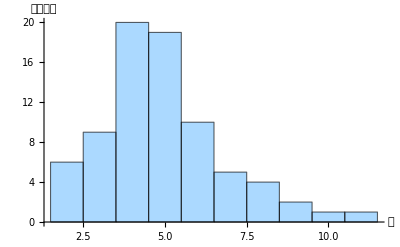
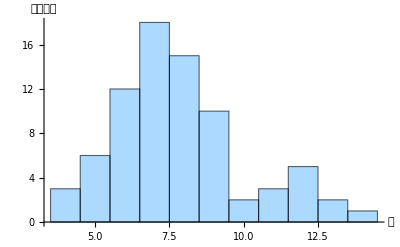
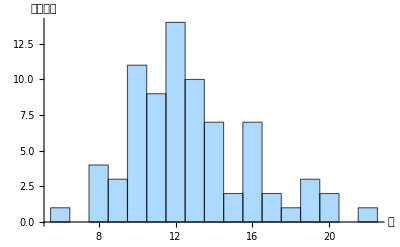

図17

主要obsolete論文の指標年

[ここまで作業済み]

### 7. 累積世代ごとのレファレンスネットワークの変化と主要論文の寄与

#### 7.1 累積世代ごとのレファレンスネットワーク構造の変化

ここではレファレンスネットワーク構造の変化を計量的に観察する。レファレンスネットワークの構造として想定されるものは、下位分野に対応するいくつかのサブネットワークの構成である。サブネットワークに該当する構造として弱連結グラフ（Weakly connected graph: WCG）を利用する。弱連結グラフとは共引用もしくは書誌結合によって連結される論文集合である。累積世代ごとのWCGに関する各特徴量を表9にを示す。この表はレファレンス情報をもとに構成しているため、レファレンスを持たず引用もされない論文は集計されていない。そこで「Largest WCG vertices % (all articles)」には全論文から再計算した割合を示す。Zipfの係数aについても全論文から再計算したがほぼ変化が見られなかったため記載していない。

全体の傾向として累積世代が進むに伴いWCGの数も増加するが最大WCGのメンバー数も急増する。この相乗効果によりグループを構成するメンバー数の差はより顕著になる。このことはZipfの係数aが累積世代が進むごとに増加していることからもわかる。一方で最大WCGのサイズ（論文数）も累積世代が進むにつれ増加し、2020にはそのメンバー数は全論文の6割に達している。

表9

累積世代ごとのレファレンスネットワークの属性:

論文数、WCG数、最大WCGにおける論文数（そのパーセンテージ）、すべての論文を対象にした場合の最大WCGにおける論文数のパーセンテージ、WCGを構成する論文数におけるZipfの係数a。

Generation | WCG vertices | Lone vertices | WCG | Largest WCG vertices | Largest WCG vertices % | Largest WCG vertices % (all articles) | Zipf's a
1946-1950 | 25659 | 296336 | 2353 | 17910 | 69.8 | 5.4 | 7.51
1946-1955 | 106865 | 774662 | 3851 | 94830 | 88.7 | 10.9 | 11.26
1946-1960 | 230664 | 1203519 | 4624 | 216474 | 93.8 | 15.3 | 12.1
1946-1965 | 387646 | 1774556 | 5729 | 370660 | 95.6 | 17.3 | 13.4
1946-1970 | 635815 | 2542940 | 7020 | 615244 | 96.8 | 19.5 | 13.94
1946-1975 | 991194 | 3356424 | 8446 | 966113 | 97.5 | 22.3 | 13.13
1946-1980 | 1452803 | 4248958 | 9401 | 1425267 | 98.1 | 25.1 | 13.7
1946-1985 | 2022734 | 5222321 | 10026 | 1993398 | 98.5 | 27.6 | 14.18
1946-1990 | 2761367 | 6403037 | 10687 | 2730892 | 98.9 | 29.9 | 14.7
1946-1995 | 3715190 | 7594669 | 11361 | 3683220 | 99.1 | 32.7 | 15.4
1946-2000 | 4704818 | 9000206 | 12147 | 4670358 | 99.3 | 34.2 | 15.4
1946-2005 | 6388248 | 10294609 | 13000 | 6351561 | 99.4 | 38.2 | 17.27
1946-2010 | 9604916 | 10857321 | 13398 | 9568400 | 99.6 | 46.9 | 17.87
1946-2015 | 14351433 | 11071404 | 13643 | 14315982 | 99.8 | 56.4 | 18.64
1946-2020 | 20271870 | 11229183 | 14933 | 20235562 | 99.8 | 64.4 | 19.1

#### 7.2 レファレンスネットワークの成長の様相

ここでは累積世代間のネットワークの差分を見ることにより、レファレンスネットワークの成長を捉える。成長をノードの発生、エッジの発生、これらによるネットワーク全体の構造変化ととらえ、構造変化に関してはWCGの結合に注目する。ノードの発生については新規出版と同義であるため特に言及しない。以下ではエッジの発生とWCGの結合に関する次の項目を調査する。

新規に発生した引用数

新規に発生した引用により結合が発生した前世代WCG数

新規に発生した引用に関して異なる前世代WCGを結合(引用)する論文の数

新規に発生した引用により異なる前世代WCGと結合された前世代WCG数

また、以上とは別にWCGの結合における主要論文の寄与を調べる。

##### 7.2.1 世代間で新たに発生した引用関係とこれにより結合されるWCG

6.2に挙げた項目の調査結果を表9に示す。新規に発生する引用やWCGの結合に寄与する論文は出版される論文の増加にともない増加する傾向にある。一方、他のWCGと結合されるWCGの割合は幅があるものの一定の傾向を見せている。

表9

累積世代間のレファレンスネットワークの差分に関する属性

累積世代 | 新規に発生した引用数 | 新規に発生した引用のうち
主要論文に対する引用数(%) | 新規に発生した引用に関して
異なる前世代WCGを結合する論文の数 | 新規に発生した引用により
結合が発生した前世代WCG数 | 新規に発生した引用により
異なる前世代WCGと結合された前世代WCG数 | 前世代WCG数 | WCGの結合率
1955 | 148555 | 718 (0.5) | 1632 | 1280 | 909 | 2353 | 0.39
1960 | 291655 | 3109 (1.1) | 1942 | 1485 | 1185 | 3851 | 0.31
1965 | 445022 | 8846 (2.) | 1717 | 1297 | 1070 | 4624 | 0.23
1970 | 818629 | 26986 (3.3) | 1937 | 1411 | 1133 | 5729 | 0.2
1975 | 1369688 | 43178 (3.2) | 2240 | 1549 | 1306 | 7020 | 0.19
1980 | 1998678 | 54563 (2.7) | 2520 | 1716 | 1500 | 8446 | 0.18
1985 | 2821649 | 103101 (3.7) | 2480 | 1683 | 1478 | 9401 | 0.16
1990 | 4022714 | 230540 (5.7) | 2438 | 1553 | 1392 | 10026 | 0.14
1995 | 5715688 | 221170 (3.9) | 2345 | 1450 | 1310 | 10687 | 0.12
2000 | 6095490 | 153837 (2.5) | 1603 | 1147 | 1048 | 11361 | 0.09
2005 | 9616785 | 103356 (1.1) | 2553 | 1508 | 1353 | 12147 | 0.11
2010 | 27854672 | 221562 (0.8) | 6243 | 2576 | 2407 | 13000 | 0.19
2015 | 63696093 | 1530822 (2.4) | 11124 | 3404 | 3235 | 13398 | 0.24
2020 | 98878679 | 5603859 (5.7) | 11676 | 3472 | 3255 | 13643 | 0.24

##### 7.2.2 WCGの結合における主要論文の寄与

主要論文は常に最大WCGにのみ出現している。このためWCGの結合は主要論文間の共引用によるものは存在しないが、主要論文とそれ以外の論文の共引用によるWCGの結合は発生している。この発生に関する引用数を表10に示す。

主要論文とそれ以外の論文の共引用のみによるWCGの結合は未調査である。

表10

累積世代間の主要論文とそれ以外の論文の共引用数とそれによるWCGの結合

## 考察・まとめ

### 1. 収録の変化

本研究では75年間にわたる収録期間を対象としているため、収録ポリシーの変更など学術活動とは異なる要因による変化が含まれている。この傍証としてはZipfの係数の変化が挙げられる。一般的に学術的生産にかかるZipfの係数変化は増加傾向をなすと考えられるが、図3では1980を前後として上昇傾向から下降傾向へと急激に変化しており何らかの収録上の要因によるものと思われる。

論文の収録数は2005ころから急激な上昇が見られ、新規主要論文の出現においも2010より急激な上昇がみられる。このことは収録対象が急速に拡大したためと思われるが、ポリシーの変更等ではなく実際の雑誌の新生、あるいは各雑誌における収録論文数の増加を反映したものであるかもしれない。

一方、本研究では研究トレンドの分析にMeSHを用いているため、HeSHの変更・追加は本研究の分析に大きく影響するが、NLMでは伝統的に遡及的な変更を行うため、世代によよる差異という影響は少ないと考えられる。すなわち、本研究の主眼である研究トレンドの「変化」という視点においては一定の視点からの分析が行われたと考えて良いであろう。

### 2. 研究テーマの変化

表6および表7ともに主要なテーマはほとんどすべて生化学・分子生物学に関するもので、しかもかなり一般的なターム（Humans、Animals、Proteinsなど）として現れている。表6（主要論文）に特徴的に見られるタームとして、Epoxy Resins、Molybdenum、Tungstenといったものがあり歯学にかかるテーマであると推察される。

### 3. レファレンスネットワークの変化

## 参考

Leydesdorf, L. Various methods for the mapping of science. Scientometrics. 1987, Vol. 11, Nos 5-6, p. 295-324.

Leydesdorf, L. Clusters and maps of science journals based on bi-connected graphs in Journal Citation Reports. Journal of Docu- mentation. 2004, Vol. 60, No. 4, p. 371-427.

Leydesdorf, L. Indicators of structual change in the dynamics of science: Entropy statisitics of the SCI Journal Citation Re- ports. Scientometrics. 2002, Vol. 53, No. 1, p. 131-159.

Leydesdorf L. Can scientific journals be classified in terms of aggregated journal- journal citation relations using the Journal Citation Reports? Journal of the American Society for Information Science and Tech- nology. 2006, Vol. 57, No. 5, p. 601-613.

天野晃;児玉閲;柴田大輔;小野寺夏生. 引用データに基づく自然科学領域における学術研究分野間の関係. 情報メディア研究. 2013, Vol 12, No. 1, p. 28-41.

天野晃;児玉閲. 引用にもとづく雑誌クラスタリング法の開発. 情報メディア研究. 2008, Vol 7, No. 1, p. 63-73.

Li

https://pubmed.ncbi.nlm.nih.gov/ . (accessed 2024.07.01)
P.D.B. Parolo, et.al. Attention decay in science. Journal of Informatics. Vol.9, p.734-745. 2015.

## 検討

Essential journalsの過去のIF <- 困難

Clustering -> 可視化が困難なのでクラスタリングで工夫するしかない

article <- 困難かも

cited/citing -> modularityによるコミュニティ発見はできるかも

MeSH

journal

cited/citing

MeSH

MeSH

article cited/citing

article内共出現

Network構造分析

Networkにおけるcentralityの偏り

Network成長の可視化 (reference) <- なんらかの捨象・クラスタリングが必要 -> 難しい

article

Journal

MeSH

Essential articlesが構成する「Essential network」を抽出できるか？

グラフ(vertex)の差分に注目する

top 1%を元にネットワークを再構築する

メンバーのtop1%を考慮する

表6、7のタームの頻度を考慮する

ジニ計数 : 集中度がサチるので、別の指標の方がよい、尖度が良いか？

グラフ複雑性

graphRedundancyComplexity[g_Graph] := Module[{vc, ec, ecmean, etp},
  vc = VertexCount[g] // N;
  ec = EdgeCount[g] // N;
  ecmean = ec/(vc^2);
  etp = Entropy[AdjacencyMatrix[g] // Flatten] // N;
  (vc) (vc^ecmean) Exp[etp]
  ]